```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
HedgeChart[stock_,inverse_,start_,end_]:=Module[{s1,s2,portfolio},
s1=NormalizeData[stock,start,end];
s2=NormalizeData[inverse,start,end];
portfolio=Transpose@{s2[[All,1]],Mean/@Transpose@{s1[[All,2]],s2[[All,2]]}};
DateListPlot[{s1,s2,portfolio},PlotLegends->{stock,inverse,stock<>" & "<>inverse},PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20}]
]
```

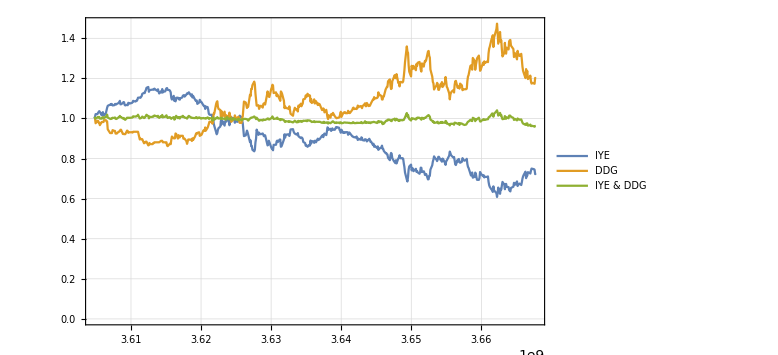

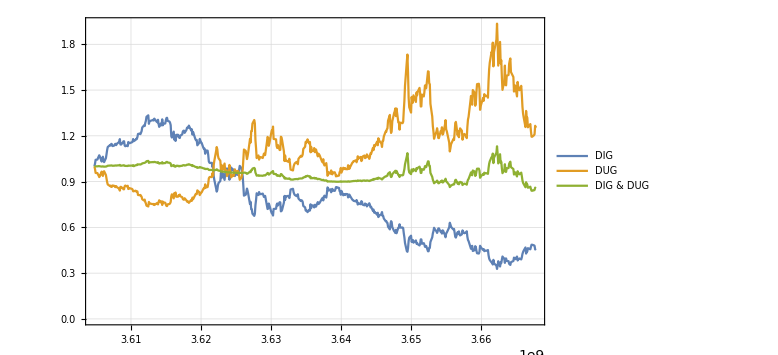

```mathematica
start=DatePlus[Today,-Quantity[2,"Years"]];
chart1=HedgeChart["IYE","DDG",start,Today]
chart2=HedgeChart["DIG","DUG",start,Today]
```

```mathematica
Export[NotebookDirectory[]<>"iye_ddg.png",Magnify@chart1];
Export[NotebookDirectory[]<>"dig_dug.png",Magnify@chart2];
```

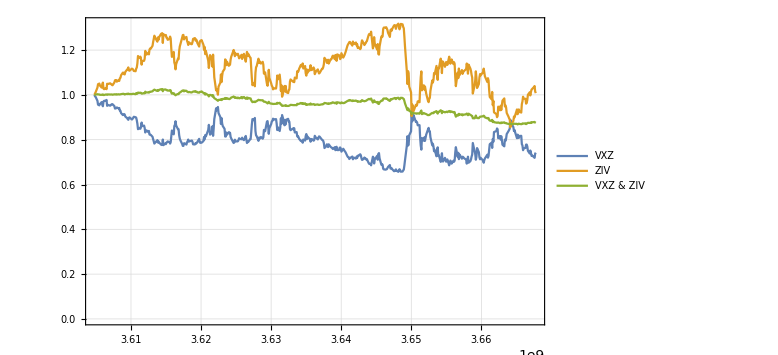

```mathematica
HedgeChart["VXZ","ZIV",start,Today]
```

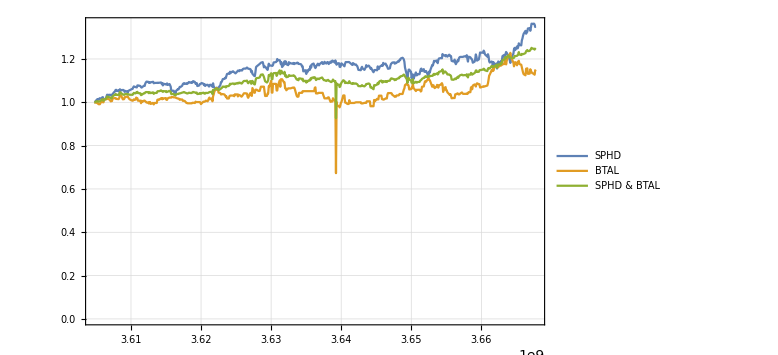

```mathematica
HedgeChart["SPHD","BTAL",start,Today]
```

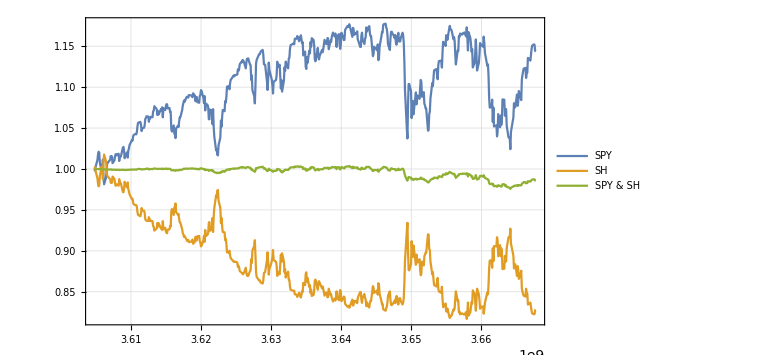

```mathematica
HedgeChart["SPY","SH",start,Today]
```

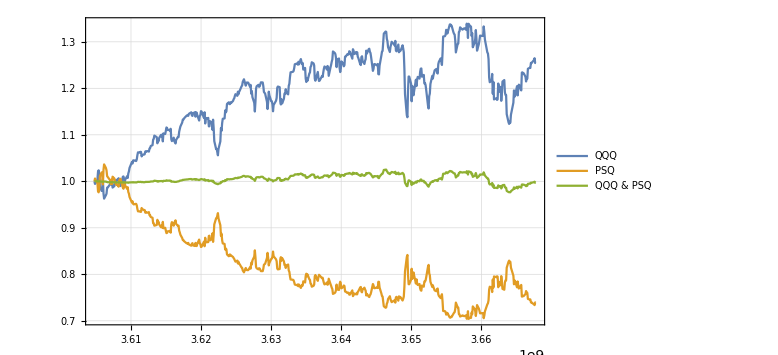

```mathematica
HedgeChart["QQQ","PSQ",start,Today]
```

```mathematica
HedgeChart["IYE","DDG",start,Today]
```

-Graphics-

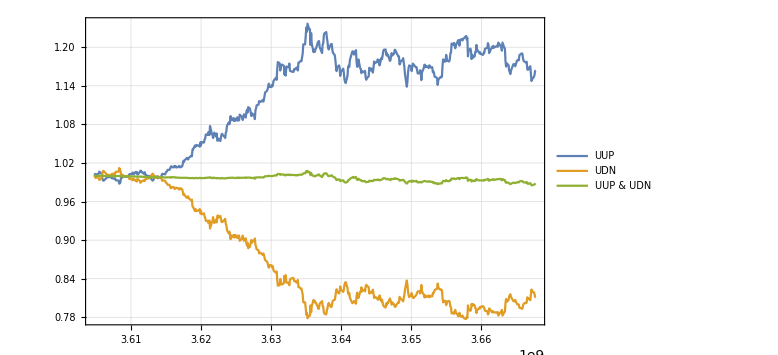

```mathematica
HedgeChart["UUP","UDN",start,Today]
```

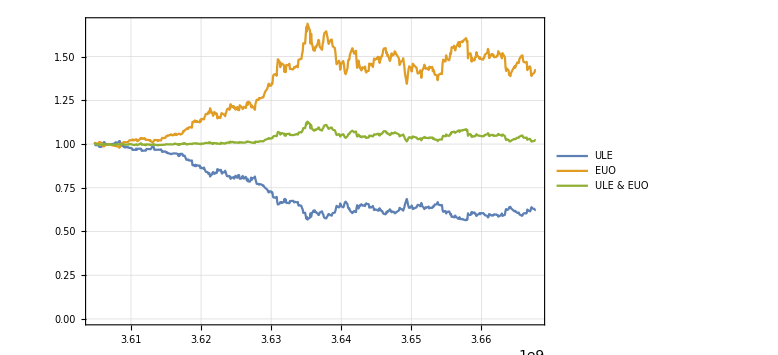

```mathematica
HedgeChart["ULE","EUO",start,Today]
```

```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
BTALChart[stock_,inverse_,start_,end_]:=Module[{btal,invalid,s1,s2,portfolio,portfolio2},
btal=NormalizedData["BTAL",start,end];
invalid=First@FirstPosition[btal[[All,1]],_?(#=={2015,4,29}&)];
btal=Delete[btal,invalid];
s1=NormalizeData[stock,start,end]//Delete[#,invalid]&;
s2=NormalizeData[inverse,start,end]//Delete[#,invalid]&;
portfolio=Transpose@{s1[[All,1]],Mean/@Transpose@{btal[[All,2]],s1[[All,2]]}};
portfolio2=Transpose@{s1[[All,1]],Mean/@Transpose@{s2[[All,2]],s1[[All,2]]}};
DateListPlot[{btal,s1,s2,portfolio,portfolio2},PlotLegends->{"BTAL",stock,inverse,"BTAL & "<>stock,inverse<>" & "<>stock},PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20}]
]
```

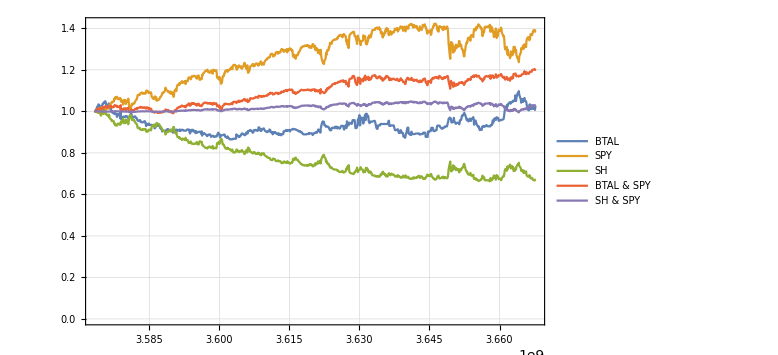

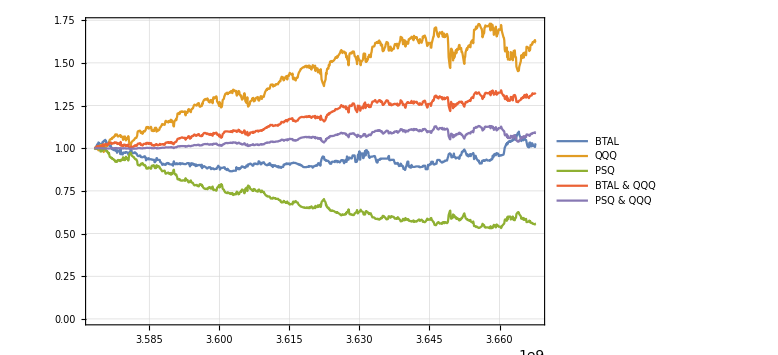

```mathematica
start=DatePlus[Today,-Quantity[3,"Years"]];
chart1=BTALChart["SPY","SH",start,Today]
chart2=BTALChart["QQQ","PSQ",start,Today]
```

```mathematica
Export[NotebookDirectory[]<>"chart1.png",Magnify@chart1];
Export[NotebookDirectory[]<>"chart2.png",Magnify@chart2];
```